```mathematica
<<ACPackages`
```

```mathematica
SetWorkDir["2009.10.04/1"]
```

D:\Home\Anton\programs\torMHD\2009.10.04\1

```mathematica
SetWorkDir["2009.09.23"]
```

D:\Home\Anton\programs\torMHD\2009.09.23

```mathematica
SetWorkDir["Debug"]
```

d:\home\Anton\programs\torMHD\Debug

```mathematica
$HistoryLength=0;
```

### Чтение списков

```mathematica
Off[Thread::tdlen];
lv=ReadList["vv.dat"];lv=Map[{#⟦1,1⟧,#⟦2⟧}&,lv];
ltm=Flatten[First/@lv];
{Length[ltm],Last[ltm]}
```

{203,5.82×10^-6}

```mathematica
PrintRange[{First[#],Max[Last[#]]}&/@lv,All,PlotLabel->"Maximum of stream velocity"]
```

```mathematica
Export["energy5.dat",Transpose@Join[{ltm},Map[Last,{mp,mdp,mvx,mdvx,mvy,mdvy,mvz,mdvz,mAx,mdAx,mAy,mdAy,mAz,mdAz,mBx,mBy,mBz,mqp,mqvx,mqvy,mqvz,mqAx,mqAy,mqAz,mqBx,mqBy,mqBz},{2}]]]
```

```mathematica
PrintRange[dif[ltm],All,PlotLabel->"Time step"]
PrintRange[{#⟦1⟧/3,#⟦2⟧}&/@(mqvx+mqvy+mqvz)]
```

```mathematica
len=Transpose[Import["energy.dat","Table"]];
```

```mathematica
len=Transpose[Select[Import["energy.dat","Table"],(First[#]>0)&]];
ltm=First[len];PrintRange[Transpose[{Drop[ltm,1],dif[ltm]}],All,PlotLabel->"Time step. Last="<>ToString[Last[ltm]]]
{mp,mdp,mvx,mdvx,mvy,mdvy,mvz,mdvz,mAx,mdAx,mAy,mdAy,mAz,mdAz,mBx,mBy,mBz,mqp,mqvx,mqvy,mqvz,mqAx,mqAy,mqAz,mqBx,mqBy,mqBz}=Transpose[{ltm,#}]&/@Drop[len,2];
(*PrintRange[{#⟦1⟧/3,#⟦2⟧}&/@(mqvx+mqvy+mqvz)]*)
PrintRange[{#⟦1⟧/3,Log[10,#⟦2⟧]}&/@(mqvx+mqvy+mqvz),All,PlotLabel->"Last energy="<>ToString[Last[Last[mqvx+mqvy+mqvz]]]]
PrintRange[{#⟦1⟧/3,Log[10,#⟦2⟧]}&/@(mqBx+mqBy+mqBz),All,
PlotLabel->"Last energy="<>ToString[Last[Last[mqBx+mqBy+mqBz]]]]
```

```mathematica
ListPlot[mqvx+mqvy+mqvz]
```

```mathematica
ListLogPlot[mqBx+mqBy+mqBz]
```

```mathematica
ListLogPlot[mqBx+mqBy+mqBz+mqvx+mqvy+mqvz]
```

```mathematica
MapThread[PrintRange[#1,All,PlotLabel->#2]&,
{Map[Function[l,{l⟦1⟧,Log[l⟦2⟧]/2}],#]&/@{mqvx,mqvy,mqvz,mqp},{"Mean quadratic of vr","Mean quadratic of vϕ","Mean quadratic of vz","Mean quadratic of p"}}]
```

```mathematica
grs=MapThread[PrintRange[#1,All,PlotLabel->#2]&,{Map[Function[l,{l⟦1⟧,Log[l⟦2⟧]/2}],#]&/@{mqAx,mqAy,mqAz},{"Mean quadratic of Ar","Mean quadratic of Aϕ","Mean quadratic of Az"}}]
```

```mathematica
MapThread[PrintRange[#1,All,PlotLabel->#2]&,{Map[Function[l,{l⟦1⟧,Log[Abs[l⟦2⟧]]/2}],#]&/@{mdAx,mdAy,mdAz},{"Difference of Ar","Difference of Aϕ","Difference of Az"}}]
```

```mathematica
MapThread[PrintRange[#1,All,PlotLabel->#2]&,{Map[Function[l,{l⟦1⟧,Log[Abs[l⟦2⟧]]/2}],#]&/@{mdvx,mdvy,mdvz,mdp},{"Difference of vr","Difference of vϕ","Difference of vz","Difference of pressure"}}]
```

```mathematica
grs=MapThread[PrintRange[#1,Automatic,PlotLabel->#2]&,{dif[Map[Function[l,{l⟦1⟧,Log[l⟦2⟧]/2}],#]]&/@{mqBx,mqBy,mqBz},{"difMean quadratic of Br","difMean quadratic of Bϕ","difMean quadratic of Bz"}}]
```

```mathematica
PrintRange@Select[Function[l,{l⟦1⟧,Log[l⟦2⟧]/2}]/@mqBy,First[#]>0.0&]
```

```mathematica
grs=MapThread[PrintRange[#1,All,PlotLabel->#2]&,{Map[Function[l,{l⟦1⟧,Log[Abs[l⟦2⟧]]}],#]&/@{mAx,mAy,mAz},{"Maximum of Ar","Maximum of Aϕ","Maximum of Az"}}]
```

```mathematica
grs=MapThread[PrintRange[#1,Automatic,PlotLabel->#2]&,{Map[Function[l,{l⟦1⟧,10^Log[10,Abs[l⟦2⟧]]}],#]&/@{mvx,mvy,mvz,mp},{"Maximum of vr","Maximum of vϕ","Maximum of vz","Maximum of pressure"}}]
```

```mathematica
grs=MapThread[PrintRange[#1,Automatic,PlotLabel->#2]&,{Map[Function[l,{l⟦1⟧,Log[10,Abs[l⟦2⟧]]}],#]&/@{mBx,mBy,mBz},{"Point of Br","Point of Bϕ","Point of Bz"}}]
```

```mathematica
ListLogPlot[mqBx]
```

### Чтение снимков

```mathematica
HarmClearance[l_]:=Divide@@Take[Sort[Take[Abs@Fourier@l,Ceiling[Length[l]/2]]],-2]
```

```mathematica
out=.;ReadBinarySnapFiles["ponom_","_39152.snp",6,out,PrintInfo->None];
{coor,bounds,node}=ReadAuxFiles[{"coord","node"},ShiftVector->{0,0,0},ProcDistrib->{4,1,4},NumberOfRefs->4];
{Bx,By,Bz}=rotc[Sequence@@Take[out,-3],3];
PrintRange[WithoutFict@Bx⟦10,All,25⟧]
PrintRange[Take[Abs@Fourier@WithoutFict@Bx⟦15,All,15⟧,14]]
-10Log[10,HarmClearance[WithoutFict@Bx⟦13,All,8⟧]]
```

17.613

```mathematica
EstimateBoundary/@{Bx,By,Bz}
```

{127.803,0.992457,21.2705}

```mathematica
{p1,vx1,vy1,vz1,Axm1,Aym1,Azm1,nutm1}={p,vx,vy,vz,Axm,Aym,Azm,nutm};
{p1,vx1,vy1,vz1,Ax1,Ay1,Az1,nut1}={p,vx,vy,vz,Ax,Ay,Az,nut};
```

```mathematica
{p1,vx1,vy1,vz1,Ax1,Ay1,Az1,nut1}=out;
```

```mathematica
{p2,vx2,vy2,vz2,Ax2,Ay2,Az2,nut2}=out;
```

```mathematica
Max/@Abs[{p1,vx1,vy1,vz1,Ax1,Ay1,Az1,nut1}-{p2,vx2,vy2,vz2,Ax2,Ay2,Az2,nut2}]
```

{1.,1.5,1.,1.9,1.03193,1.0119,1.03194,1.}

```mathematica
GetInner[ar_?ArrayQ]:=Block[{b},Switch[Length[Dimensions[ar]],3,Transpose[(node/.b_:>BitAnd[b,8])/8#&/@Transpose[ar]],2,(node/.b_:>BitAnd[b,8])/8 ar,_,$Failed]]
```

```mathematica
GetVacuum[ar_?ArrayQ]:=Block[{b},Switch[Length[Dimensions[ar]],3,Transpose[(1-(node/.b_:>BitAnd[b,8])/8)#&/@Transpose[ar]],2,(1-(node/.b_:>BitAnd[b,8])/8)ar,_,$Failed]]
```

```mathematica
<<ACPackages`Master`
```

```mathematica
Remove[PrintInfo]
```

```mathematica
out=.;ReadBinarySnapFile["velocity.snp",3,out,PrintInfo->Debug];
```

{1,1,1}

{5.00004,76241,64,64,64,100.}

Length of read from binary=1029000 and size of it=4116000 bytes

ghost=3

```mathematica
out=ReadList["pumpflow.dmp"];
```

```mathematica
out=.;ReadBinarySnapFile["screw_2_103547.snp",6,out,PrintInfo->Automatic];
{coor,bounds,node}=ReadAuxFiles[{"coord","node"},ShiftVector->{0,0,0},ProcDistrib->{1,1,2},NumberOfRefs->4];
Print[bounds];
```

```mathematica
out=.;ReadBinarySnapFile["screw_64_184434.snp",6,out,PrintInfo->Automatic];
{coor,bounds,node}=ReadAuxFiles[{"coord","node"},ShiftVector->{0,0,0},ProcDistrib->{2,16,2},NumberOfRefs->4];
Print[bounds];
```

{2,16,2}

{29.9001,184434,64,64,64,300.}

ghost=3

{{-2.,2.},{0.,6.283},{-2.,2.}}

```mathematica
If[Length[out]>6,out=Take[out,{2,-2}]];
If[Length[out]>7,out=Take[out,{1,-2}]];
```

```mathematica
out=.;ReadBinarySnapFiles["screw",".bak",8,out,PrintInfo->None];
(*{vx,vy,vz,Ax,Ay,Az}=out;*)
{coor,bounds,node}=ReadAuxFiles[{"coord","node"},ShiftVector->{0,0,0},ProcDistrib->{2,4,2},NumberOfRefs->4];
```

```mathematica
ArrayPlot[Transpose[#[[All,5]]]]&/@out
```

```mathematica
ArrayPlot[out[[4,All,5]]/.{0.->0},PlotRange->All]
```

```mathematica
{Bx,By,Bz}=rotc[Ax,Ay,Az,3];
```

```mathematica
{Bx,By,Bz}=rotd[Sequence@@Take[out,-3],3];
(*{jx,jy,jz}=rotc[Bx,By,Bz,3];*)
```

```mathematica
{p,vx,vy,vz,Ax,Ay,Az,nut}=ReadTextSnapFile["pumpflow_1_0.snp",8,PrintInfo->Automatic];
{coor,bounds,node}=ReadAuxFiles[{"coord","node"},ShiftVector->{0,0,0},ProcDistrib->{1,1,1},NumberOfRefs->4];
```

{1,1,1}

{0.,0,32,32,32,10.}

ghost=3

```mathematica
Max/@Abs/@{p,vx,vy,vz,Ax,Ay,Az,nut}
```

```mathematica
out=.;ReadBinarySnapFile["velocity.snp",4,out,PrintInfo->None];
```

```mathematica
Max[Abs[Flatten[#]]]&/@out
```

{0.267323,0.311311,0.260178,0.149289,0.0466989,0.144551}

```mathematica
√Mean[Flatten[#^2]]&/@out
```

```mathematica
Max@Abs@√Total[Take[out,{1,3}]^2]
```

```mathematica
EstimateBoundary[mat_?ArrayQ]:=Block[{Ein,Eb,ds=Dimensions[mat]},
(*Ein=Mean[Flatten@mat⟦2;;-2,All,2;;-2⟧^2];
Eb=√(((Times@@ds) Mean[Flatten@mat^2]-(Times@@(ds-2))Ein)/((Times@@ds)-(Times@@(ds-2))));
Eb/Max[Flatten@Abs@mat]*)
(Max@Abs@Flatten@mat⟦2;;-2,All,2;;-2⟧)/(Max@Abs@Complement[Flatten@mat,Flatten@mat⟦2;;-2,All,2;;-2⟧])
]
```

```mathematica
PrintRange[WithoutFict@Bx⟦10,All,25⟧]
```

```mathematica
PrintRange[Take[Abs@Fourier@WithoutFict@Bx⟦15,All,15⟧,10]]
```

```mathematica
ReadDrawSection["dynamo_2_12820.snp",Binary,8,{5,6,7}]
```

```mathematica
DrawSection[Sequence@@ReadSection[4314]]
```

```mathematica
Table[ListPlot3D[Cut3D[Az,2,i],PlotRange->All],{i,1,Dimensions[By][[2]]}]
```

```mathematica
out1=out;
```

```mathematica
Max[Abs[Flatten[#]]]&/@(out1-out)
```

{0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
{p2,vx2,vy2,vz2,Ax2,Ay2,Az2,nut2,Axm2,Aym2,Azm2,nutm2}={p,vx,vy,vz,Ax,Ay,Az,nut,Axm,Aym,Azm,nutm};
```

```mathematica
Max[Abs[#]]&/@({p2,vx2,vy2,vz2,Ax2,Ay2,Az2,nut2,Axm2,Aym2,Azm2,nutm2}-{p1,vx1,vy1,vz1,Ax1,Ay1,Az1,nut1,Axm1,Aym1,Azm1,nutm1})
```

{0.,0.,0.,0.,0.,0.,0.,0,0.,0.,0.,0.}

```mathematica
({p2,vx2,vy2,vz2,Ax2,Ay2,Az2,nut2,Axm2,Aym2,Azm2,nutm2}=={p1,vx1,vy1,vz1,Ax1,Ay1,Az1,nut1,Axm1,Aym1,Azm1,nutm1})
```

True

```mathematica
Max/@{vx,vy,vz}
```

{3.32433,0.999996,2.06709}

### Построение трёхмерных графиков

```mathematica
ListPlot3D/@Cut3D/@Drop[out,0]
```

```mathematica
Show2x[ListPlot3D[Transpose[Cut3D[#,2,7]],PlotRange->All,DisplayFunction->Identity]&,
Take[out,4]]
```

```mathematica
ListContourPlot[WithoutFict@out[[5,All,60]],ContourLabels->True]
```

```mathematica
ListContourPlot[out[[1,All,5]]/.{0.->1},PlotRange->All]
```

```mathematica
Show2x[ListPlot3D[Transpose[Cut3D[#,2,4]],PlotRange->All]&,{Bx,By,Bz,vx}]
```

```mathematica
Table[ListPlot3D[Transpose[Cut3D[Bz,2,i]],PlotRange->All,DisplayFunction->Identity],{i,36}]
```

```mathematica
ListPlot3D[Transpose[Cut3D[out⟦5⟧,2,7]],PlotRange->All,DisplayFunction->Identity]
```

```mathematica
Show2x[ListPlot3D[Cut3D[#,2,4],DisplayFunction->Identity,PlotRange->All]&,{Bx,By,Bz,Last[out]}]
```

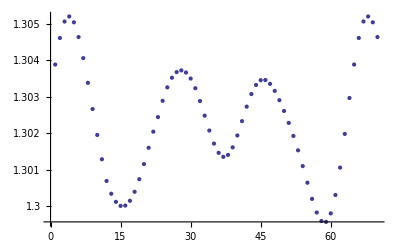

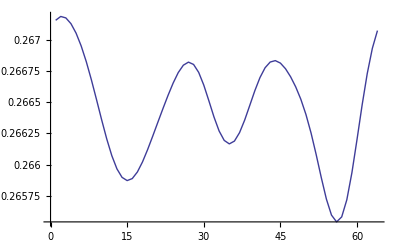

```mathematica
ListLogPlot[Max/@Flatten/@Transpose[out[[1]]]]
ListLogPlot[WithoutFict@√(Mean/@((Flatten/@Transpose[out[[1]]])^2)),Joined->True]
```

```mathematica
DrawSection[Sequence@@Take[GetInner/@out,{1,3}],PointOfSections->{1.5,0,0}]
```

```mathematica
DrawSection[vx,vy,vz,PointOfSections->{0.5,0,0}]
```

```mathematica
ListStreamPlot[Transpose[out⟦1;;3;;2,All,10⟧,{3,1,2}]]
```

```mathematica
DrawSection[Bx,By,Bz,PointOfSections->{0.5,0,0}]
```

```mathematica
{jx,jy,jz}=rotd[Bx,By,Bz,ghost];
```

```mathematica
DrawSection[jx,jy,jz,PointOfSections->{0.5,0,0}]
```

```mathematica
(*Show4[ListPlot3D[Transpose[Cut3D[#]],PlotRange->All,DisplayFunction->Identity]&,{vx,vy,vz,√(vx^2+vy^2+vz^2)}];*)
Show2x[ListPlot3D[Transpose[Cut3D[#]],PlotRange->All,DisplayFunction->Identity,Mesh->False]&,{Ax,Ay,Az,nut}]
Show2x[ListPlot3D[Transpose[Cut3D[WithoutFict[#]]],PlotRange->All,DisplayFunction->Identity,Mesh->False]&,{Bx,By,Bz,√(Bx^2+By^2+Bz^2)}]
Show2x[ListPlot3D[Transpose[Cut3D[WithoutFict[#]]],PlotRange->All,DisplayFunction->Identity,Mesh->False]&,{jx,jy,jz,√(jx^2+jy^2+jz^2)}]
```

```mathematica
dist=15;PrintRange[Cut3D[Cut3D[Bx,3,dist],1,dist]]
```

```mathematica
(*ListPlot3D[Transpose[Cut3D[Ay/coor⟦1⟧-PD[Ax,ghost,dx⟦2⟧,2]/coor⟦1⟧]]];
ListPlot3D[Transpose[Cut3D[PD[Ay,ghost,dx⟦1⟧,1]]]];*)
```

```mathematica
(*Brfi[r1_,fi1_,z1_]=ReplaceAll[1/r∂_fi Azi[r,fi,z]-∂_z Ayi[r,fi,z],{r->r1,fi->fi1,z->z1}];
Bϕfi[r1_,fi1_,z1_]=ReplaceAll[∂_z Axi[r,fi,z]-∂_r Azi[r,fi,z],{r->r1,fi->fi1,z->z1}];
Bzfi[r1_,fi1_,z1_]=ReplaceAll[∂_r Ayi[r,fi,z]-1/r∂_fi Axi[r,fi,z]+1/r Ayi[r,fi,z],{r->r1,fi->fi1,z->z1}];
Bzfi[r1_,fi1_,z1_]=ReplaceAll[1/r∂_r (r Ayi[r,fi,z])-1/r∂_fi Axi[r,fi,z],{r->r1,fi->fi1,z->z1}];*)
```

```mathematica
{vxi,vyi,vzi,pi,Axi,Ayi,Azi,Bxi,Byi,Bzi,jxi,jyi,jzi,nuti}=ListInterpolation[#,{{Min[coor⟦1⟧],Max[coor⟦1⟧]},{Min[coor⟦2⟧],Max[coor⟦2⟧]},{Min[coor⟦3⟧],Max[coor⟦3⟧]}},InterpolationOrder->1]&/@{vx,vy,vz,p,Ax,Ay,Az,Bx,By,Bz,jx,jy,jz,nut};
```

```mathematica
Show[GraphicsRow[{SectionRZ[vxi,vyi,vzi,0.2 π],SectionRΦ[vxi,vyi,vzi,Mean[bounds⟦3⟧],AspectRatio->Automatic],SectionΦZ[vxi,vyi,vzi,Mean[bounds⟦1⟧],AspectRatio->Automatic]},Spacings->Scaled[0.]],AspectRatio->1]
```

```mathematica
Show[GraphicsRow[{SectionRZ[Bxi,Byi,Bzi,1.8],SectionRΦ[Bxi,Byi,Bzi,Mean[bounds⟦3⟧],AspectRatio->Automatic],SectionΦZ[Bxi,Byi,Bzi,Mean[bounds⟦1⟧],AspectRatio->Automatic]},Spacings->Scaled[0.]],AspectRatio->1]
```

```mathematica
Show[GraphicsRow[{SectionRZ[jxi,jyi,jzi,0.3 π],SectionRΦ[jxi,jyi,jzi,Mean[bounds⟦3⟧]],SectionΦZ[jxi,jyi,jzi,Mean[bounds⟦1⟧]]},Spacings->Scaled[0.]],AspectRatio->1,ImageSize->1000]
```

### Анимация сечений

```mathematica
{coor,bounds}=ReadAuxFiles[{"coord"},ShiftVector->{0,0,0},ProcDistrib->{2,16,2},NumberOfRefs->4];
```

```mathematica
ReadSection[iter_,nproc_Integer:1,fluct_:False]:=Block[{dump,str=ToString[iter],Ax,Ay,Az},
(*While[StringLength[str]<5,str="0"<>str];*)
(*dump=.;ReadBinarySnapFiles["ponom_","_"<>str<>".snp",7,dump,PrintInfo->None];*)
dump=.;ReadBinarySnapFile["screw_"<>ToString[nproc]<>"_"<>str<>".snp",6,dump,PrintInfo->None];
If[!NameQ[coor]∨Length[coor]=!=3,{coor,bounds}=ReadAuxFiles[{"coord"},ShiftVector->{0,0,0},ProcDistrib->{2,16,2},NumberOfRefs->4]];
(*Return[Take[dump,{1,-1}]];*)
{Ax,Ay,Az}=Take[dump,-3];
If[fluct,
{Ax,Ay,Az}-=Transpose[Table[coor⟦1,i⟧Cos[coor⟦2,j⟧]{Sin[coor⟦2,j⟧],Cos[coor⟦2,j⟧],0},{i,1,n1+2ghost},{j,1,n2+2ghost},{k,1,n3+2ghost}],{2,3,4,1}]];
(*Return[{Bx,By,Bz}=rotd[Ax,Ay,Az,ghost]];*)
{Bx,By,Bz}=rotd[Ax,Ay,Az,ghost];
(*{jx,jy,jz}=rotc[Bx,By,Bz,ghost];*)
Return[Join[Take[dump,3],{Bx,By,Bz}]];];
```

```mathematica
ReadZipSnap[iter_,nproc_Integer:1]:=Block[{temp,out},
name="screw";
temp=First[Import[name<>"_"<>ToString[nproc]<>"_"<>ToString[iter]<>".snp.zip",{"*.snp","Binary"}]];
Export[name<>"_"<>ToString[nproc]<>"_"<>ToString[iter]<>".snp",temp,"Binary","DataFormat"-> "Byte"];
out=ReadSection[iter,nproc];
Close[name<>"_"<>ToString[nproc]<>"_"<>ToString[iter]<>".snp"];
DeleteFile[name<>"_"<>ToString[nproc]<>"_"<>ToString[iter]<>".snp"];
Return[out]
];
```

```mathematica
grtot={};
```

```mathematica
nameexp="parker";
```

```mathematica
Block[{g,dump},dump=ReadList["runtest1.dmp"];np=dump⟦3⟧;KolProc=Times@@np;dump=Drop[dump,{3}];{t,count,n1,n2,n3,Rey}=Take[dump,6];dump=Drop[dump,6];{pm,vxm,vym,vzm,Axm,Aym,Azm,nutm}=Transpose[Partition[dump,8]];ghost=(Total[(Last[Dimensions[#1]]&)/@CutList[pm,Last[np]]]-n3)/(2 Last[np]);coor=ReadList["coord",Number,RecordLists->True];bounds=({1/2 (#1⟦ghost⟧+#1⟦ghost+1⟧),1/2 (#1⟦-ghost⟧+#1⟦-ghost-1⟧)}&)/@coor;Ax=First[Fold[Map[Function[m,Clue[m,#2,ghost]],Partition[#1,np⟦#2⟧],{1}]&,Axm,{1,2,3}]];Ay=First[Fold[Map[Function[m,Clue[m,#2,ghost]],Partition[#1,np⟦#2⟧],{1}]&,Aym,{1,2,3}]];Az=First[Fold[Map[Function[m,Clue[m,#2,ghost]],Partition[#1,np⟦#2⟧],{1}]&,Azm,{1,2,3}]];{Ax,Ay,Az}-=Transpose[Table[coor⟦1,i⟧ Cos[coor⟦2,j⟧] {Sin[coor⟦2,j⟧],Cos[coor⟦2,j⟧],0},{i,1,n1+2 ghost},{j,1,n2+2 ghost},{k,1,n3+2 ghost}],{2,3,4,1}];{Bx,By,Bz}=rotc[Ax,Ay,Az,ghost];{jx,jy,jz}=rotc[Bx,By,Bz,ghost];{Bxi,Byi,Bzi,jxi,jyi,jzi}=(ListInterpolation[#1,{{Min[coor⟦1⟧],Max[coor⟦1⟧]},{Min[coor⟦2⟧],Max[coor⟦2⟧]},{Min[coor⟦3⟧],Max[coor⟦3⟧]}},InterpolationOrder->1]&)/@{Bx,By,Bz,jx,jy,jz};g=GraphicsRow[{SectionRZ[Bxi,Byi,Bzi,0.2 π],SectionRΦ[Bxi,Byi,Bzi,Mean[bounds⟦3⟧]],SectionΦZ[Bxi,Byi,Bzi,Mean[bounds⟦1⟧]]},Spacings->Scaled[0.],PlotLabel->"t="<>ToString[t]];
fname=nameexp<>"0000.gif";
Export[fname,g,ImageResolution->300,ImageSize->640];]
```

```mathematica
ReadSection[697,64]//Dimensions
```

{6,70,70,70}

```mathematica
ReadZipSnap[557,64]//Dimensions
```

```mathematica
nums=Union[ToExpression[First[StringCases[#,RegularExpression["([^_]+?)_([^_]+?)_([^\\.]+?)\\.(.*?)"]->"$3"]]]&/@FileNames["*.snp"]]
{nproc}=Union[ToExpression[First[StringCases[#,RegularExpression["([^_]+?)_([^_]+?)_([^\\.]+?)\\.(.*?)"]->"$2"]]]&/@FileNames["*.snp"]]
```

{64}

```mathematica
nums=Drop[nums,64];
```

```mathematica
Monitor[res={};Do[AppendTo[res,ReadSection[nums⟦i⟧,nproc]],{i,Length[nums]}];,nums⟦i⟧]
Dimensions[res]
```

{39,6,70,70,70}

```mathematica
DrawSection[Sequence@@Take[res[[3]],{2,4}],PointOfSections->{0.5,0,0}]
```

```mathematica
DrawSection[Sequence@@res[[First@First@Position[nums,7033]]],PointOfSections->{0.5,0,0}]
```

```mathematica
Manipulate[ListLogPlot[Max/@Flatten/@Transpose[res[[i,1]]]],{i,1,Length[nums],1}]
```

```mathematica
Manipulate[DrawSection[Sequence@@res[[i,1;;3]],PointOfSections->{0.5,0,0}]/.{(PlotLabel->_String)->(PlotLabel->nums[[i]])},{i,1,Length[nums],1}]
```

```mathematica
Manipulate[{ListStreamPlot[Transpose[res⟦i,1;;3;;2,All,10⟧,{3,1,2}]],PrintRange[res⟦i,2,All,10,35⟧]},{i,1,Length[nums],1}]
```

```mathematica
PrintRange[Log[Max/@Transpose[res[[5,5]]]]]
```

```mathematica
ListPlot3D[res[[1,All,8]]/.{0.->0},PlotRange->All]
```

```mathematica
ArrayPlot[Cut3D[GetInner[res[[3,6]]],2,1],PlotRange->All]
```

```mathematica
Monitor[Do[
res=ReadSection[nums⟦i⟧,nproc];
Export["velocity"<>ToString[nums⟦i⟧]<>".gif",DrawSection[Sequence@@Take[res,{1,3}],PointOfSections->{0.5,0,0}],ImageResolution->300,ImageSize->640];
Export["magnetic"<>ToString[nums⟦i⟧]<>".gif",DrawSection[Sequence@@Take[res,-3],PointOfSections->{0.5,0,0}],ImageResolution->300,ImageSize->640],{i,Length[nums]}];,nums⟦i⟧]
```

```mathematica
Import@Last@FileNames["velocity*.gif"]
```

```mathematica
Export["velocity.gif",Flatten[Import/@Take[SortBy[FileNames["velocity*.gif"],ToExpression[First[StringCases[#,RegularExpression["velocity(\\d*?).gif"]->"0$1"]]]&],50]]]
```

```mathematica
Do[Export["velocity"<>ToString[nums⟦i⟧]<>".gif",DrawSection[Sequence@@Take[res⟦i⟧,{1,3}],PointOfSections->{0.5,0,0}],ImageResolution->300,ImageSize->640],{i,Length[nums]}]
```

```mathematica
Do[Export["magnetic"<>ToString[nums⟦i⟧]<>".gif",DrawSection[Sequence@@Take[res⟦i⟧,-3],PointOfSections->{0.5,0,0}],ImageResolution->300,ImageSize->640],{i,Length[nums]}]
```

```mathematica
ListPlot3D/@Cut3D/@res
```

```mathematica
lf1=lf2=lf3=lf4=lf5={};
Monitor[Do[Block[{Bx,By,Bz,g1,g2,fname},
{Bx,By,Bz}=ReadSection[nums⟦i⟧];
(*Print["have read ponom_"<>ToString[nums⟦i⟧]<>".snp"];*)
AppendTo[lf1,Fourier@WithoutFict@Bx⟦15,All,15⟧];
AppendTo[lf2,Fourier@(Total[Flatten[#^2]]&/@Transpose[WithoutFict@Bx,{2,1,3}])];
AppendTo[lf3,Fourier@(Total[Flatten[#^2]]&/@Transpose[WithoutFict@By,{2,1,3}])];AppendTo[lf4,Fourier@(Total[Flatten[#^2]]&/@Transpose[WithoutFict@Bz,{2,1,3}])];
],{i,1,Length[nums]}],nums⟦i⟧];
```

```mathematica
Monitor[Do[Block[{Bx,By,Bz,jx,jy,jz,g1,g2,fname},
{Bx,By,Bz}=ReadSection[nums⟦i⟧];
{jx,jy,jz}=rotc[Bx,By,Bz,3];
(*Print["have read ponom_"<>ToString[nums⟦i⟧]<>".snp"];*)
g1=DrawSection[Bx,By,Bz];
g2=DrawSection[jx,jy,jz];
fname="ponom"<>ToString[nums⟦i⟧]<>"_B.gif";
Export[fname,g1,ImageResolution->300,ImageSize->640];
fname="ponom"<>ToString[nums⟦i⟧]<>"_j.gif";
Export[fname,g2,ImageResolution->300,ImageSize->640];
],{i,1,Length[nums]}],nums⟦i⟧];
```

```mathematica
Do[Block[{g},
temp=First[Import["dynamo_2_"<>ToString[nums⟦i⟧]<>".snp.ZIP",{"*.snp","Binary"}]];
Export["dynamo_2_"<>ToString[nums⟦i⟧]<>".snp",temp,"Binary","DataFormat"-> "Byte"];
{Bx,By,Bz}=ReadSection[nums⟦i⟧];
Print["have read dynamo_2_"<>ToString[nums⟦i⟧]<>".snp"];
Close["dynamo_2_"<>ToString[nums⟦i⟧]<>".snp"];
DeleteFile["dynamo_2_"<>ToString[nums⟦i⟧]<>".snp"];
(*{Bxi,Byi,Bzi,jxi,jyi,jzi}=(ListInterpolation[#1,{{Min[coor⟦1⟧],Max[coor⟦1⟧]},{Min[coor⟦2⟧],Max[coor⟦2⟧]},{Min[coor⟦3⟧],Max[coor⟦3⟧]}},InterpolationOrder->1]&)/@{Bx,By,Bz,jx,jy,jz};g=DisplayTogetherArray[SectionRZ[Bxi,Byi,Bzi,0.2 π],SectionRΦ[Bxi,Byi,Bzi,Mean[bounds⟦3⟧]],SectionΦZ[Bxi,Byi,Bzi,Mean[bounds⟦1⟧]],Spacings->Scaled[0.],DisplayFunction->Identity,PlotLabel->"t="<>ToString[t]];*)
g=DrawSection[Bx,By,Bz];
fname="dynamo"<>ToString[nums⟦i⟧]<>".gif";Export[fname,g,ImageResolution->300,ImageSize->640];],{i,1,Length[nums]}];
```

```mathematica
gr=Table[{Bx,By,Bz,jx,jy,jz}=ReadSection[i];{Bxi,Byi,Bzi,jxi,jyi,jzi}=(ListInterpolation[#1,{{Min[coor⟦1⟧],Max[coor⟦1⟧]},{Min[coor⟦2⟧],Max[coor⟦2⟧]},{Min[coor⟦3⟧],Max[coor⟦3⟧]}},InterpolationOrder->1]&)/@{Bx,By,Bz,jx,jy,jz};DisplayTogetherArray[SectionRZ[Bxi,Byi,Bzi,0.2 π],SectionRΦ[Bxi,Byi,Bzi,Mean[bounds⟦3⟧]],SectionΦZ[Bxi,Byi,Bzi,Mean[bounds⟦1⟧]],Spacings->Scaled[0.],DisplayFunction->Identity],{i,10,2820,10}];
```

```mathematica
grtot=First/@gr
```

```mathematica
Export["current.gif",Show[#,DisplayFunction->Identity]&/@gr,ConversionOptions->{"AnimationDisplayTime"->0.2},ImageResolution->300,ImageSize->640];
```

### Изоповерхности

#### Навороченное

```mathematica
{cont1,cont2}=0.1{Max[#],Min[#]}&[By]
```

{0.0129781,-0.0129684}

```mathematica
bounds
```

{{-2.,2.},{0.,6.283},{-2.,2.}}

```mathematica
{Bxi,Byi,Bzi}=(ListInterpolation[#1,{{Min[coor⟦1⟧],Max[coor⟦1⟧]},{Min[coor⟦2⟧],Max[coor⟦2⟧]},{Min[coor⟦3⟧],Max[coor⟦3⟧]}},InterpolationOrder->1]&)/@{Bx,By,Bz};
```

```mathematica
cubic=Table[Block[{r=√(x^2+y^2),f=ArcTan[y,x+10^-10]+π},If[z≤bounds⟦3,2⟧∧z≥bounds⟦3,1⟧∧r≤bounds⟦1,2⟧∧r≥bounds⟦1,1⟧,Byi[r,f,z],0]],{z,-1.5,1.5,0.1},{x,-6,6,0.2},{y,-6,6,0.2}];
```

```mathematica
g1=ColorLighting[ListContourPlot3D[cubic,Contours->{cont1}],{1,0,0}];
g2=ColorLighting[ListContourPlot3D[cubic,Contours->{cont2}],{0,0,1}];
```

```mathematica
Show[Prepend[ListContourPlot3D[cubic,Contours->{cont1}],Opacity[0.5]]]
```

```mathematica
ListContourPlot3D[By,Contours->{cont1,cont2},ContourStyle->{Directive[Yellow,Opacity[0.8]],Directive[Pink,Opacity[0.8]]},BoxRatios->Automatic,Mesh->False,AxesLabel->{x,y,z},DataRange->bounds]
```

```mathematica
Show[g1,Lighting->Automatic]
```

```mathematica
Show[Graphics3D[EdgeForm[]],g1,g2,Lighting->None]
```

```mathematica
Show[Graphics3D[EdgeForm[]],ColorLighting[ListContourPlot3D[cubic,Contours->{cont1},DisplayFunction->Identity],{1,0,0}],ColorLighting[ListContourPlot3D[cubic,Contours->{cont2},DisplayFunction->Identity],{0,0,1}],Lighting->None]
```

#### Простое рисование поверхностей

```mathematica
{Bx,By,Bz}=WithoutFict/@{Bx,By,Bz};
```

```mathematica
{vx,vz}=out[[2;;4;;2]];
```

```mathematica
mx=Max[√(By^2)]
gh=ListContourPlot3D[By,Contours->{-1,1}mx/2,ContourStyle->{Directive[Yellow,Opacity[0.8]],Directive[Pink,Opacity[0.8]]},BoxRatios->Automatic,Mesh->False,AxesLabel->{z,y,x},DataRange->bounds]
```

0.500488

```mathematica
mx=Max[√(vz^2+vx^2)];
gh=ListContourPlot3D[√(vx^2+vz^2),Contours->{-1,1}mx/1.5,ContourStyle->{Directive[Yellow,Opacity[0.8]],Directive[Pink,Opacity[0.8]]},BoxRatios->Automatic,Mesh->False,AxesLabel->{z,y,x},DataRange->bounds]
```

```mathematica
Export["magnRe70Rm1000.eps",gh,ImageSize->300];
```

### Просмотр массива типов ячеек и отражений

```mathematica
{node}=ReadAuxFiles[{"node"}];
```

```mathematica
{coor,bounds,node,{rr,rz,mrr,mrz}}=ReadAuxFiles[{"coord","node","ref"},NumberOfRefs->4,ProcDistrib->{1,2,2}];
```

```mathematica
Union[Flatten[node]]-32
```

{-28,4,8,12,20}

```mathematica
ArrayPlot[Transpose[Map[BitAnd[Round[#1],32]&,node,{2}]],FrameTicks->True,Mesh->True,Frame->True]
```

```mathematica
flag=8+64;
ListDensityPlot[Transpose[Map[BitAnd[Round[#1],flag]&,nm⟦2⟧,{2}]]]
ListDensityPlot[Transpose[Map[BitAnd[Round[#1],flag]&,nm⟦1⟧,{2}]]]
```

```mathematica
ghost=3;
n1=First[Dimensions[node]]-2ghost
```

32

```mathematica
gc=Graphics[Circle[{n1/2+ghost+2 1/2,n1/2+ghost+2 1/2},n1/4]];
gc3d=ParametricPlot3D[{n1/2+ghost+1/2+n1/4 Sin[t],n1/2+ghost+1/2+n1/4 Cos[t],30},{t,0,2π},Axes->False,Boxed->False];
```

```mathematica
grnode[type_]:=ListPointPlot3D[BitAnd[node,type],ColorFunction->(Hue[1-#3]&),ViewPoint->{0,0,∞},PlotStyle->PointSize[Large]]
```

```mathematica
DisplayTogether[ListContourPlot[node],gc];
```

```mathematica
{Min[#],Max[#]}&/@Transpose[Most/@({rr[[First[#],Last[#]]],rz[[First[#],Last[#]]],1}&/@Position[node,52]+1)]
```

{{12.028,26.972},{12.028,26.972}}

```mathematica
Show[grnode[52],Graphics3D[Point[{rr[[First[#],Last[#]]],rz[[First[#],Last[#]]],1}&/@Position[node,52]+1]],gc3d,PlotRange->All]
```